```mathematica
NS["update_2units"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\neurobayes\\"
```

C:\Users\pglpm\repositories\neurobayes\

```mathematica
xlogy[x_,y_]:=If[x>0,x*Log[x/y],0];entr[p1_,p2_]:=Total[MapThread[xlogy,{p1,p2}]];
entr2[p1_,p2_]:=Total[MapThread[xlogy,{p2,p1}]];
```

```mathematica
values=Flatten@Import["states2n_values.csv"];
pos=Flatten@Import["states2n_pos.csv"];
n=Max[pos]
```

417461

```mathematica
nstates=Range[0,3];states=SparseArray[pos->values];
```

```mathematica
frequencies[ss_,nn_]:=Pick[Join[#[[2]],{0,0,0,0}],Join[#[[1]],Range[0,3]],ss][[1]]&@T@Tally[states[[;;nn]]]
```

```mathematica
prob[ss_,nn_,la_,ff_]:=(la*ff+frequencies[ss,nn])/(la+nn);
SetAttributes[prob,Listable];
tprob[nn_,la_,ff_]:=prob[nstates,nn,la,ff];
```

```mathematica
finfreqs=Table[frequencies[s,n]/n,{s,0,3}];
```

```mathematica
points=Round@Range[1,1000,1000/50];
```

```mathematica
FS[(nb-(la*na+lb*nb)/(la+lb))/nb]
```

(la (-na+nb))/((la+lb) nb)

```mathematica
Solve[Abs[FS[(nb-(la*na+lb*nb)/(la+lb))/nb]/.{la->10^-9,na->1/4}]==1/10,lb]
```

{{lb→(5-22 nb)/(2000000000 nb)},{lb→(-5+18 nb)/(2000000000 nb)}}

```mathematica
Table[{tprob[i,4,1/4],tprob[i,10^-9,1/4]},{i,20}]//N//MF
```

((0.2
0.2
0.4
0.2) | (2.5×10^-10
2.5×10^-10
1.
2.5×10^-10)
(0.333333
0.166667
0.333333
0.166667) | (0.5
1.25×10^-10
0.5
1.25×10^-10)
(0.428571
0.142857
0.285714
0.142857) | (0.666667
8.33333×10^-11
0.333333
8.33333×10^-11)
(0.375
0.125
0.375
0.125) | (0.5
6.25×10^-11
0.5
6.25×10^-11)
(0.444444
0.111111
0.333333
0.111111) | (0.6
5.×10^-11
0.4
5.×10^-11)
(0.5
0.1
0.3
0.1) | (0.666667
4.16667×10^-11
0.333333
4.16667×10^-11)
(0.545455
0.0909091
0.272727
0.0909091) | (0.714286
3.57143×10^-11
0.285714
3.57143×10^-11)
(0.583333
0.0833333
0.25
0.0833333) | (0.75
3.125×10^-11
0.25
3.125×10^-11)
(0.615385
0.0769231
0.230769
0.0769231) | (0.777778
2.77778×10^-11
0.222222
2.77778×10^-11)
(0.642857
0.0714286
0.214286
0.0714286) | (0.8
2.5×10^-11
0.2
2.5×10^-11)
(0.666667
0.0666667
0.2
0.0666667) | (0.818182
2.27273×10^-11
0.181818
2.27273×10^-11)
(0.6875
0.0625
0.1875
0.0625) | (0.833333
2.08333×10^-11
0.166667
2.08333×10^-11)
(0.705882
0.0588235
0.176471
0.0588235) | (0.846154
1.92308×10^-11
0.153846
1.92308×10^-11)
(0.722222
0.0555556
0.166667
0.0555556) | (0.857143
1.78571×10^-11
0.142857
1.78571×10^-11)
(0.736842
0.0526316
0.157895
0.0526316) | (0.866667
1.66667×10^-11
0.133333
1.66667×10^-11)
(0.75
0.05
0.15
0.05) | (0.875
1.5625×10^-11
0.125
1.5625×10^-11)
(0.761905
0.047619
0.142857
0.047619) | (0.882353
1.47059×10^-11
0.117647
1.47059×10^-11)
(0.772727
0.0454545
0.136364
0.0454545) | (0.888889
1.38889×10^-11
0.111111
1.38889×10^-11)
(0.782609
0.0434783
0.130435
0.0434783) | (0.894737
1.31579×10^-11
0.105263
1.31579×10^-11)
(0.791667
0.0416667
0.125
0.0416667) | (0.9
1.25×10^-11
0.1
1.25×10^-11))

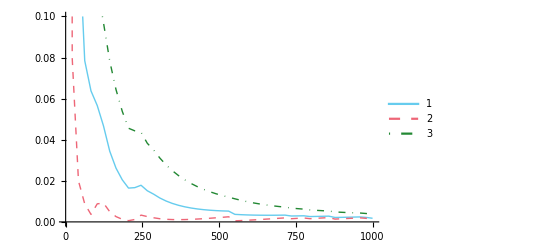

```mathematica
ListPlot[T@Table[{entr[tprob[i,4,Table[1/4,{4}]],finfreqs],entr[tprob[i,0.001,Table[1/4,{4}]],finfreqs],entr[tprob[i,40,{75,10,10,5}/100],finfreqs]},{i,points}],DataRange->{1,1000},PlotStyle->{Thick,Dashed,DotDashed},PlotLegends->Auto,Joined->True,PlotRange->{0,0.1}]
```

```mathematica
states[[300]]
```

0

```mathematica
xlogy[2,0]
```

∞

```mathematica
SparseArray[{states[[300]]+1->1}]
```

SparseArray[…]

```mathematica
occur[i_]:=SparseArray[{states[[i]]+1->1},{4}];
```

```mathematica
occur[500]//MF
```

(1
0
0
0)

```mathematica
t={0,0,0,0};t[[2]]=1;t
```

{0,1,0,0}

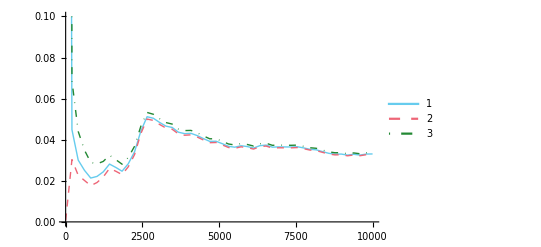

```mathematica
rg=10000;points=Round@Range[1,rg,rg/50];ListPlot[T@Table[{entr2[tprob[i,4,Table[1/4,{4}]],occur[i]],entr2[tprob[i,0.001,Table[1/4,{4}]],occur[i]],entr2[tprob[i,40,{75,10,10,5}/100],occur[i]]},{i,points}],DataRange->{1,rg},PlotStyle->{Thick,Dashed,DotDashed},PlotLegends->Auto,Joined->True,PlotRange->{0,0.1}]
```

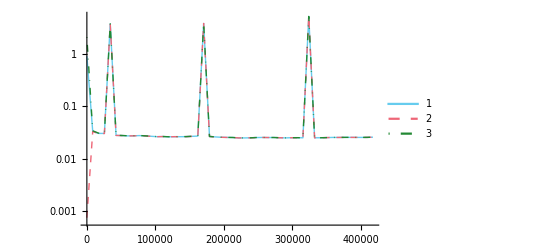

```mathematica
rg=n;points=Round@Range[1,rg,rg/50];ListLogPlot[T@Table[{entr2[tprob[i,4,Table[1/4,{4}]],occur[i]],entr2[tprob[i,0.001,Table[1/4,{4}]],occur[i]],entr2[tprob[i,40,{75,10,10,5}/100],occur[i]]},{i,points}],DataRange->{1,rg},PlotStyle->{Thick,Dashed,DotDashed},PlotLegends->Auto,Joined->True,PlotRange->Auto]
```

```mathematica
entr[tprob[1000,100,{40,10,10,5}/100],finfreqs]//N
```

-0.0157273

```mathematica
tprob[1000,100,{40,10,10,5}/100]
```

{1021/1100,13/1100,13/550,1/220}

```mathematica
Total@%
```

213/220

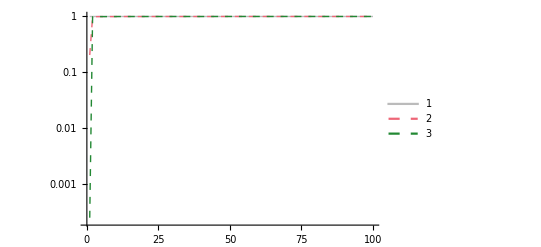
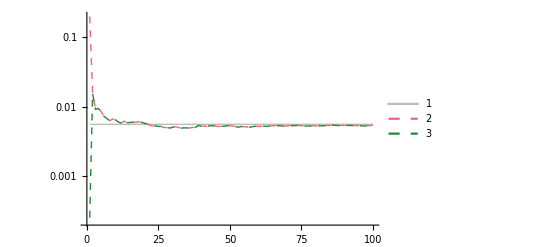
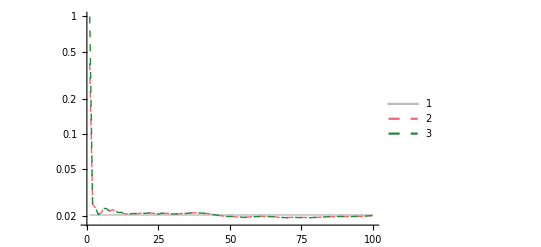
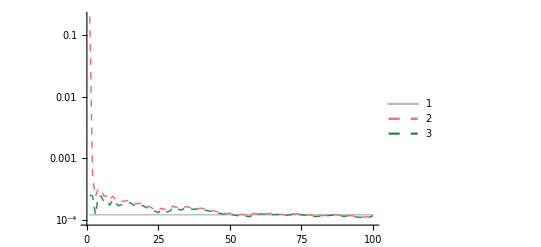
(-Graphics-
-Graphics-
-Graphics-
-Graphics-)

```mathematica
Table[ListLogPlot[{finfreqs[[s+1]]*Table[1,{Length@points}],Table[prob[s,i,4,1/4],{i,points}],Table[prob[s,i,0.001,1/4],{i,points}]},PlotStyle->{{grey,Thick},Dashed,Dashed},PlotLegends->Auto,Joined->True,PlotRange->Auto],{s,0,3}]//MF
```

```mathematica
prob[1,1,4,1/4]
```

1/5

```mathematica
T@Tally@states
```

{{2,0,1,3},{8541,406553,2317,50}}

```mathematica
{}+{0}
```

{}+{0}